```mathematica
V1[r,Fa]
```

-1/r+If[0≤r<1,-2.7156298495422798770722075365871798715065108699048,0]

## Definition

```mathematica
δ50V
```

{-0.0010111998140872207752808208261703652631523828719599,-0.0031976800235278821815007097532292797715298185928745,-0.010111491731830732719170441925669522776415359340761,-0.031960789405125522933373507687582716449828744781774,-0.10060964977929146302920898313696792694331731557305,-0.30401507950111997826713021892165681010205303319686,-0.73208746431028526245311528777683686832243445809232,1.57076844873560063803161059293930907694661482058,0.016604178728464292214601585968525799790046011557589,-0.88670402762674631122717109111765016717471389247589,-0.20298505215399587250713295435250322849670206154992,0.68169074216635950683681615527649603106534146201229,-0.14617618177335730464091724674502957670008967138439,0.55098654513026699261247024430075427761020475265127,-1.069259789592027712878623874602989877147311062589,1.47161864503671708577806852705949807570607304415,-0.032187824893958698621560949873406331585183920121249,-0.7662901597075154258059144113406261328686158728487,-1.0748683557181722316154300446515310649841369657651}

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
a=1;ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V2[r_,Fc_,Fd_]=-α/r+Fc E^(-Fd r)/r;
V3[r_,Fe_,Fh_]=-α/r+Fe(E^(-Fh r^2))/r;
```

```mathematica
Fa=-2.71562984954227987707220753658717987150651086990482099679916347484158640580824`50.;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[evShifted],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},{opt___},{opt2nd___}]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1},opt2nd]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)]]
```

```mathematica
δexpminus10=δ50e[10^-10,V1[r,Fa]]
δexpminus5=δ50e[10^-5,V1[r,Fa]]
δ50V=δ50[V1[r,Fa]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031976961469011990340175947388312022842768758134) is less than WorkingPrecision (50.).

End with 0.3790719s

-0.00031976960379102838045407775954520831798758975488105

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095049698306647997185436012980973711952116617) is less than WorkingPrecision (50.).

End with 0.2656285s

-0.10060964977929146302920898313696792694331731557305

NDSolve::precw: The precision of the differential equation ({{2 (0.001+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587464132865018998597875314097697935557) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898684) is less than WorkingPrecision (50.).

End with 0.3437522s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031971676417742421692484655632768966490285659951) is less than WorkingPrecision (50.).

End with 0.3593805s

{1/1000000000,-0.0010111998140872207752808208261703652631523828719599}    0.343752

End with 0.3906280s

{0.001,-0.73208746431028526245311528777683686832243445809232}    0.359381

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22631) is less than WorkingPrecision (50.).

{1/1000000,-0.031960789405125522933373507687582716449828744781774}    0.390628

NDSolve::precw: The precision of the differential equation ({{2 (0.003+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 0.4531288s

{0.01,-0.88670402762674631122717109111765016717471389247589}    0.468758

NDSolve::precw: The precision of the differential equation ({{2 (0.03+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031976909224997864261154138264165866246216981177) is less than WorkingPrecision (50.).

End with 0.3593801s

{1/100000000,-0.0031976800235278821815007097532292797715298185928745}    0.369629

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095049698306647997185436012980973711952116617) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==35870.5) is less than WorkingPrecision (50.).

End with 0.3725799s

End with 0.4008247s

{1/100000,-0.10060964977929146302920898313696792694331731557305}    0.377585

{0.003,1.57076844873560063803161059293930907694661482058}    0.406829

NDSolve::precw: The precision of the differential equation ({{2 (0.007+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.20582) is less than WorkingPrecision (50.).

End with 0.4832275s

{0.03,-0.20298505215399587250713295435250322849670206154992}    0.489352

NDSolve::precw: The precision of the differential equation ({{2 (0.07+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010111836353197228798292517594804279873741813862) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.3580371s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.3137410221526808473123574012541655877376698201) is less than WorkingPrecision (50.).

{1/10000000,-0.010111491731830732719170441925669522776415359340761}    0.36304

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0166057) is less than WorkingPrecision (50.).

End with 0.3561076s

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.3+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000,-0.30401507950111997826713021892165681010205303319686}    0.357232

End with 0.3904847s

{0.007,0.016604178728464292214601585968525799790046011557589}    0.390485

FindRoot::precw: The precision of the argument function (Tan[δ]==0.811462) is less than WorkingPrecision (50.).

End with 0.4644147s

{0.07,0.68169074216635950683681615527649603106534146201229}    0.464415

NDSolve::precw: The precision of the differential equation ({{2 (0.1+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.614463) is less than WorkingPrecision (50.).

End with 0.7187421s

{0.3,0.55098654513026699261247024430075427761020475265127}    0.7343687

NDSolve::precw: The precision of the differential equation ({{2 (0.7+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.147226) is less than WorkingPrecision (50.).

End with 0.7187547s

{0.1,-0.14617618177335730464091724674502957670008967138439}    0.7187547

FindRoot::precw: The precision of the argument function (Tan[δ]==10.04983271206702846207961618022003619570185374) is less than WorkingPrecision (50.).

End with 1.2187819s

{1,1.47161864503671708577806852705949807570607304415}    1.2344

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.82382) is less than WorkingPrecision (50.).

End with 0.9218837s

{0.7,-1.069259789592027712878623874602989877147311062589}    0.937507

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.03219894563313406668363475666893071855716533175) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.96249605362685539392366192572858232057638771238) is less than WorkingPrecision (50.).

End with 1.5705676s

End with 2.8089678s

{3,-0.032187824893958698621560949873406331585183920121249}    1.576672

{7,-0.7662901597075154258059144113406261328686158728487}    2.826699

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.848336981536975011352598864634846824296146574) is less than WorkingPrecision (50.).

End with 2.6979273s

{10,-1.0748683557181722316154300446515310649841369657651}    2.738793

{-0.0010111998140872207752808208261703652631523828719599,-0.0031976800235278821815007097532292797715298185928745,-0.010111491731830732719170441925669522776415359340761,-0.031960789405125522933373507687582716449828744781774,-0.10060964977929146302920898313696792694331731557305,-0.30401507950111997826713021892165681010205303319686,-0.73208746431028526245311528777683686832243445809232,1.57076844873560063803161059293930907694661482058,0.016604178728464292214601585968525799790046011557589,-0.88670402762674631122717109111765016717471389247589,-0.20298505215399587250713295435250322849670206154992,0.68169074216635950683681615527649603106534146201229,-0.14617618177335730464091724674502957670008967138439,0.55098654513026699261247024430075427761020475265127,-1.069259789592027712878623874602989877147311062589,1.47161864503671708577806852705949807570607304415,-0.032187824893958698621560949873406331585183920121249,-0.7662901597075154258059144113406261328686158728487,-1.0748683557181722316154300446515310649841369657651}

## FindFit For Lepage’s Data

```mathematica
enDetermineFa[Fa_?NumberQ]:=EigenEnergySolo[V1[r,Fa],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.00129205010],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
EvaluateV1[Fa_]:=enDetermineFa[Fa]+0.00129205010;
FindRoot[enDetermineFa[Fa]==-0.00129205010,{Fa,-0.5,0.5},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{Fa,EvaluateV1[Fa]}]]
```

FindRoot::precw: The precision of the argument function (enDetermineFa[Fa]==-0.00129205) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]+If[«5»,-0.5,0]) u[r$48256]-u''[r$48256]/2==e$48255 u[r$48256],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]+If[«5»,0.5,0]) u[r$48812]-u''[r$48812]/2==e$48811 u[r$48812],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]+If[«5»,-0.5,0]) u[r$49194]-u''[r$49194]/2==e$49193 u[r$49194],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-1.388088988603454382841405464478,{0.0000119977}}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-2.064405718693868131365713093239,{4.95134×10^-6}}

{-2.539642391176148057432160445812,{1.22662×10^-6}}

{-2.69614605280816353519694135412,{1.32691×10^-7}}

{-2.715129591313698956207820834535,{3.39795×10^-9}}

{-2.715628498049126237897191872428,{9.17923×10^-12}}

{-2.7156298494490648656671861477191499021184930024878,{6.33174×10^-16}}

{-2.715629849542279877072207505228688132389911701315,{0.}}

{-2.7156298495422798770722075061126791703892488610244,{0.}}

{-2.7156298495422798770722075107528719954049550488302,{0.}}

{-2.7156298495422798770722075557205157157145468696201,{0.}}

{-2.715629849542279877072207536572507802364017270634,{0.}}

{-2.7156298495422798770722075417700884547724537828803,{0.}}

{-2.7156298495422798770722075381231861281041671080537,{0.}}

{-2.7156298495422798770722075370022609751786995001853,{0.}}

{-2.7156298495422798770722075366502158566268978535057,{0.}}

{-2.7156298495422798770722075365917355600615514350569,{0.}}

{-2.715629849542279877072207536561316332195720838129,{-2.1684×10^-19}}

{-2.7156298495422798770722075365711235158213913588178,{0.}}

{-2.7156298495422798770722075365720901499621819755325,{0.}}

{-2.7156298495422798770722075365723828862578079692004,{0.}}

{-2.7156298495422798770722075345282359924895182408982,{0.}}

{-2.7156298495422798770722075361976956475206495190519,{0.}}

{-2.7156298495422798770722075364724839201675862622526,{0.}}

{-2.7156298495422798770722075365467829450661285086453,{0.}}

{-2.7156298495422798770722075365646604757478509921229,{0.}}

{-2.7156298495422798770722075365700530619671263354388,{0.}}

{-2.7156298495422798770722075365716799812200477427304,{0.}}

{-2.7156298495422798770722075365721727081148049606565,{0.}}

{-2.7156298495422798770722075365723201060511388247441,{0.}}

{-2.7156298495422798770722075341788312750785804295286,{0.}}

{-2.7156298495422798770722075359483768908300220819023,{0.}}

{-2.7156298495422798770722075364066620667681409657849,{-2.1684×10^-19}}

{-2.7156298495422798770722075365486544870262145028306,{0.}}

{-2.7156298495422798770722075365651813638807571081896,{0.}}

{-2.7156298495422798770722075365701663960256339160983,{0.}}

{-2.7156298495422798770722075365716703509022009814481,{0.}}

{-2.7156298495422798770722075365721257966329936356668,{0.}}

{-2.7156298495422798770722075365722620059670687723181,{0.}}

{-2.7156298495422798770722075372592210356762425970087,{-2.1684×10^-19}}

{-2.7156298495422798770722075366769588596268731337376,{0.}}

{-2.715629849542279877072207536515967225635356599589,{-2.1684×10^-19}}

{-2.7156298495422798770722075365636476878484959272772,{-2.1684×10^-19}}

{-2.7156298495422798770722075365712474862019902258833,{0.}}

{-2.7156298495422798770722075365719965039284511188214,{0.}}

{-2.7156298495422798770722075365722233286377894232163,{0.}}

{-2.7156298495422798770722075377580332621442613495738,{-2.1684×10^-19}}

{-2.7156298495422798770722075366998022674429040221827,{0.}}

{-2.7156298495422798770722075365943053678292172001786,{0.}}

{-2.7156298495422798770722075365593299259074313352864,{0.}}

{-2.7156298495422798770722075365684485862977346868175,{0.}}

{-2.7156298495422798770722075365711520948389433681317,{0.}}

{-2.7156298495422798770722075365719677274624924051028,{0.}}

{-2.7156298495422798770722075365722148276545557818464,{0.}}

{-2.7156298495422798770722075378621869826354689221941,{0.}}

{-2.7156298495422798770722075368567500417708411195341,{-2.1684×10^-19}}

{-2.7156298495422798770722075366059210614786173174242,{0.}}

{-2.7156298495422798770722075365843950311978180552261,{0.}}

{-2.7156298495422798770722075365675894999835026954023,{-2.1684×10^-19}}

{-2.7156298495422798770722075365717350164200711280931,{0.}}

{-2.7156298495422798770722075365721451595298737098272,{0.}}

{-2.7156298495422798770722075365722677956294912674173,{0.}}

{-2.7156298495422798770722075385666494756931060300891,{2.1684×10^-19}}

{-2.7156298495422798770722075361458485034434823912847,{0.}}

{-2.7156298495422798770722075364691062968221949068893,{0.}}

{-2.7156298495422798770722075365412205702457924683562,{0.}}

{-2.7156298495422798770722075365630270942116651171785,{0.}}

{-2.7156298495422798770722075365699962095511107120938,{0.}}

{-2.7156298495422798770722075365716190102717118230568,{0.}}

{-2.7156298495422798770722075365721106378459207627125,{0.}}

{-2.7156298495422798770722075365722574733674050964245,{0.}}

{-2.71562984954227987707220753731280868485835839475,{0.}}

{-2.7156298495422798770722075367954233379367450269132,{0.}}

{-2.7156298495422798770722075366270209126533994695496,{-2.1684×10^-19}}

{-2.7156298495422798770722075365784642118994577406481,{0.}}

{-2.7156298495422798770722075365741557374756984460981,{0.}}

{-2.7156298495422798770722075365716005739571788307301,{0.}}

{-2.7156298495422798770722075365721051350297362734605,{0.}}

{-2.7156298495422798770722075365722558279809591240604,{0.}}

{-2.7156298495422798770722075373322616253733538091753,{0.}}

{-2.7156298495422798770722075367630567615182618146911,{0.}}

{-2.7156298495422798770722075366199568747194635971177,{0.}}

{-2.7156298495422798770722075365866519398921920727455,{0.}}

{-2.7156298495422798770722075365808687098526869807115,{0.}}

{-2.7156298495422798770722075365890247867401475093105,{0.}}

{-2.7156298495422798770722075365806677634575568021186,{0.}}

{-2.715629849542279877072207536589101562139442162408,{0.}}

{-2.7156298495422798770722075365877869652852902279008,{0.}}

{-2.7156298495422798770722075365868684183615505125011,{0.}}

{-2.7156298495422798770722075365860073572854744528197,{0.}}

{-2.7156298495422798770722075365879126736781691958275,{0.}}

{-2.7156298495422798770722075365868957146421160414582,{0.}}

{-2.7156298495422798770722075365859260803449419262622,{0.}}

{-2.7156298495422798770722075365863590366555403659727,{0.}}

{-2.7156298495422798770722075365872248273471248612981,{0.}}

{-2.7156298495422798770722075365867434854667539143124,{0.}}

{-2.7156298495422798770722075365859318779814275632003,{0.}}

{-2.7156298495422798770722075365880603041020503826456,{0.}}

{-2.7156298495422798770722075365869213210735429524905,{0.}}

{-2.7156298495422798770722075365867767494190829844113,{0.}}

{-2.7156298495422798770722075365856702366602791611688,{0.}}

{-2.7156298495422798770722075365887345492486427874946,{0.}}

{-2.7156298495422798770722075365825491145692400266741,{0.}}

{-2.7156298495422798770722075365859945923142997158317,{0.}}

{-2.7156298495422798770722075365879376415635354602601,{0.}}

{-2.7156298495422798770722075365869005424178756750946,{0.}}

{-2.715629849542279877072207536586767122264839109896,{0.}}

{-2.7156298495422798770722075365857459601140151588996,{0.}}

{-2.7156298495422798770722075365884239395985576292965,{0.}}

{-2.7156298495422798770722075365873669462653878176972,{0.}}

{-2.7156298495422798770722075365867663299885282905401,{0.}}

{-2.7156298495422798770722075365857521918515617582865,{0.}}

{-2.7156298495422798770722075365884117509853361044162,{0.}}

{-2.7156298495422798770722075365828439394000777598123,{0.}}

{-2.7156298495422798770722075365860434336489836697617,{0.}}

{-2.7156298495422798770722075365878421131281297329437,{0.}}

{-2.7156298495422798770722075365868426273897902063152,{0.}}

{-2.7156298495422798770722075365860841520441232113933,{0.}}

{-2.7156298495422798770722075365877624722951123099062,{0.}}

{-2.7156298495422798770722075365868666632586721589302,{0.}}

{-2.7156298495422798770722075365860125832499398313564,{0.}}

{-2.7156298495422798770722075365863939428311905009384,{0.}}

{-2.7156298495422798770722075365865478374410955979016,{0.}}

{-2.7156298495422798770722075365868772040739638937321,{0.}}

{-2.7156298495422798770722075365859811970976920256664,{0.}}

{-2.7156298495422798770722075365879638411768902905632,{0.}}

{-2.7156298495422798770722075365868615775022357554071,{0.}}

{-2.7156298495422798770722075365860277265117645440451,{0.}}

{-2.715629849542279877072207536587872833677042107578,{0.}}

{-2.7156298495422798770722075365868880202478267877349,{0.}}

{-2.7156298495422798770722075365859489910424481172608,{0.}}

{-2.7156298495422798770722075365863682817188296918483,{0.}}

{-2.7156298495422798770722075365872067449905109177732,{0.}}

{-2.7156298495422798770722075365867405959642671653512,{0.}}

{-2.7156298495422798770722075365859546056849973490027,{0.}}

{-2.7156298495422798770722075365880158511407126963579,{0.}}

{-2.7156298495422798770722075365869155619370486102213,{0.}}

{-2.7156298495422798770722075365861355524466332854955,{0.}}

{-2.7156298495422798770722075365876685732687888391343,{0.}}

{-2.7156298495422798770722075365868148231336432556378,{0.}}

{-2.7156298495422798770722075365867274068576349944591,{0.}}

{-2.7156298495422798770722075365878295218141669877844,{0.}}

{-2.7156298495422798770722075365869265717782061623212,{0.}}

{-2.7156298495422798770722075365864029573211141042856,{0.}}

{-2.7156298495422798770722075365873044579438893871375,{0.}}

{-2.7156298495422798770722075365868146960671345048133,{0.}}

{-2.7156298495422798770722075365867664160901834978752,{0.}}

{-2.7156298495422798770722075365865364808327011930059,{0.}}

{-2.7156298495422798770722075365870379771565809419229,{0.}}

{-2.7156298495422798770722075365867743937014612015558,{0.}}

{-2.7156298495422798770722075365867484051084846295423,{0.}}

{-2.7156298495422798770722075365866246334293113589434,{0.}}

{-2.7156298495422798770722075365866814777836031448684,{0.}}

{-2.7156298495422798770722075365888981222681426685575,{0.}}

{-2.7156298495422798770722075365830754051303973531718,{0.}}

{-2.7156298495422798770722075365861755618596807902279,{0.}}

{-2.7156298495422798770722075365876250669123388346916,{0.}}

{-2.7156298495422798770722075365868634270351737312551,{0.}}

{-2.7156298495422798770722075365864090927127520271934,{0.}}

{-2.7156298495422798770722075365872935458173157941585,{0.}}

{-2.7156298495422798770722075365868129523840671727289,{0.}}

{-2.7156298495422798770722075365863087145059652396061,{0.}}

{-2.7156298495422798770722075365865650929991112711393,{0.}}

{-2.7156298495422798770722075365869929761911234300546,{0.}}

{-2.7156298495422798770722075365862947812380360073961,{0.}}

{-2.7156298495422798770722075365874311384105079941877,{0.}}

{-2.7156298495422798770722075365868337430938682288164,{0.}}

{-2.7156298495422798770722075365862069568624911653214,{0.}}

{-2.7156298495422798770722075365875739981520081897132,{0.}}

{-2.7156298495422798770722075365868825348471258343361,{0.}}

{-2.7156298495422798770722075365867967329960148352349,{0.}}

{-2.7156298495422798770722075365867583884585597239548,{0.}}

{-2.7156298495422798770722075365865757711159348946588,{0.}}

{-2.7156298495422798770722075365869755052222638727383,{0.}}

{-2.7156298495422798770722075365863233009634575287111,{0.}}

{-2.7156298495422798770722075365873847467273778956354,{0.}}

{-2.7156298495422798770722075365868465400824794007158,{0.}}

{-2.7156298495422798770722075365864486115253564995636,{0.}}

{-2.7156298495422798770722075365871809099865064417397,{0.}}

{-2.7156298495422798770722075365867959327261246342101,{0.}}

{-2.7156298495422798770722075365867580308208353430027,{0.}}

{-2.7156298495422798770722075365865775215310192602526,{0.}}

{-2.715629849542279877072207536586976809399376712615,{0.}}

{-2.7156298495422798770722075365863211767025453767773,{0.}}

{-2.715629849542279877072207536587388201712385307628,{0.}}

{-2.7156298495422798770722075365868272552124367235974,{0.}}

{-2.7156298495422798770722075365862387110224946703292,{0.}}

{-2.715629849542279877072207536587522345167725479437,{0.}}

{-2.7156298495422798770722075365868475247457523238776,{0.}}

{-2.7156298495422798770722075365864463072183530118385,{0.}}

{-2.7156298495422798770722075365871846582932927195961,{0.}}

{-2.7156298495422798770722075365867965742456043212707,{0.}}

{-2.715629849542279877072207536586758317513574468425,{0.}}

{-2.7156298495422798770722075365865761183476833527584,{0.}}

{-2.7156298495422798770722075365869749371000786028531,{0.}}

{-2.7156298495422798770722075365863242263283789136861,{0.}}

{-2.7156298495422798770722075365873832414801997371312,{0.}}

{-2.7156298495422798770722075365868462672784722558233,{0.}}

{-2.7156298495422798770722075365864492499407432919437,{0.}}

{-2.7156298495422798770722075365871798715065108699048,{0.}}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

{Fa→-2.7156298495422798770722075365871798715065108699048}

```mathematica
Clear@Fa
```

```mathematica
enDetermineFaPS[Fa_?NumberQ]:=δ50e[ee[[1]],V1[r,Fa]];
EvaluateV1PS[Fa_]:=enDetermineFaPS[Fa]+0.000421343353;
FindRoot[enDetermineFaPS[Fa]==-0.000421343353,{Fa,-0.5,0},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{Fa,EvaluateV1PS[Fa]}]]
```

FindRoot::precw: The precision of the argument function (enDetermineFaPS[Fa]==-0.000421343) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000643938352234111549985052125046258371294338356706) is less than WorkingPrecision (50.).

End with 26.7809087s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812766364548349297845953040304157064597567381) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 19.2075488s

End with 0.2351761s

End with 0.7065111s

End with 0.5684124s

End with 0.2641886s

End with 0.2471747s

End with 0.2391802s

End with 0.2031563s

End with 0.2141639s

{-0.8191379886507282232598063506751,-0.000197681}

End with 0.2771938s

End with 0.3202392s

End with 0.2531901s

End with 0.2261584s

{-1.125734408619461450130589433124,-0.000170888}

End with 0.2281463s

End with 0.2621979s

End with 0.3352497s

End with 0.2441839s

{-1.670257852060359323370644067935,-0.000112479}

End with 0.2461792s

End with 0.2591828s

End with 0.2571929s

{-2.718851228712091702129526756099,0.000102714}

End with 0.3152228s

End with 0.2151410s

End with 0.2892171s

{-2.218346931341296086801048800776,-0.0000277189}

End with 0.2511907s

End with 0.2321775s

End with 0.2241706s

{-2.324711801921768956771454243521,-5.95992×10^-6}

End with 0.2261605s

End with 0.2681902s

End with 0.2541791s

{-2.353845779053554807689658520417,4.31998×10^-7}

End with 0.2851901s

End with 0.2682025s

End with 0.2721910s

{-2.351876756338476669367427452371,-6.34708×10^-9}

End with 0.2681971s

End with 0.2641993s

End with 0.2952209s

{-2.351905267057208332953023712729,-6.67773×10^-12}

End with 0.2682008s

End with 0.2761950s

End with 0.2852139s

{-2.35190529708477690000577516539,1.03324×10^-16}

End with 0.3542628s

End with 0.3492603s

End with 0.3552506s

{-2.351905297084312339391931523166,0.}

End with 0.2722053s

End with 0.2682021s

End with 0.2641996s

End with 0.2762024s

End with 0.2771840s

End with 0.3172373s

{-2.3519052970843123393994928034390076949716297755,0.}

{Fa→-2.3519052970843123393994928034390076949716297755}

```mathematica
δ50[V1[r,-2.35190529708431233939949280343900769497162977549998033394977614677622893314766`50.]]
```

NDSolve::precw: The precision of the differential equation ({{2 (0.003+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.07+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.13365271122231361204360713409946904999574162732) is less than WorkingPrecision (50.).

End with 0.3662455s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.32468) is less than WorkingPrecision (50.).

{1/100000,-0.13286531839349428235847254153174527329620348870557}    0.370248

End with 0.4052871s

NDSolve::precw: The precision of the differential equation ({{2 (0.001+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==8.59298) is less than WorkingPrecision (50.).

{0.01,-0.92416666455924088231664937290419816485638313028211}    0.41029

End with 0.4763236s

NDSolve::precw: The precision of the differential equation ({{2 (0.03+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.717132) is less than WorkingPrecision (50.).

{0.003,1.454943402945015570334094305826487895606152422577}    0.480326

End with 0.5744055s

NDSolve::precw: The precision of the differential equation ({{2 (0.007+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.07,0.62213160375601279849777179684623893025077135960036}    0.58041

NDSolve::precw: The precision of the differential equation ({{2 (0.1+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57674) is less than WorkingPrecision (50.).

End with 0.3872736s

{0.001,-1.0055953196859293029696091860057379106084362204191}    0.393278

NDSolve::precw: The precision of the differential equation ({{2 (0.3+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0281437) is less than WorkingPrecision (50.).

End with 0.4553217s

{0.007,-0.028136244351860985335680116092629317337120156620648}    0.461326

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.267124) is less than WorkingPrecision (50.).

End with 0.5694014s

NDSolve::precw: The precision of the differential equation ({{2 (0.7+1/r-If[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.03,-0.26102920913880719915661005732863691700202275523962}    0.576407

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.207589) is less than WorkingPrecision (50.).

End with 0.5834113s

{0.1,-0.20468184074240976852499894048030028169736567125235}    0.589416

FindRoot::precw: The precision of the argument function (Tan[δ]==0.524991) is less than WorkingPrecision (50.).

End with 0.6234395s

{0.3,0.48343969353384336122590056301948857379258413000905}    0.630447

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.1669) is less than WorkingPrecision (50.).

End with 0.9026377s

{0.7,-1.138429133423167635056728929403741826540147596823}    0.9156467

FindRoot::precw: The precision of the argument function (Tan[δ]==5.8747332128643091836681031078366394987403780689) is less than WorkingPrecision (50.).

End with 1.0737579s

{1,1.4021918750296187964077770860582089056273029668007}    1.085768

{-0.13286531839349428235847254153174527329620348870557,-1.0055953196859293029696091860057379106084362204191,1.454943402945015570334094305826487895606152422577,-0.028136244351860985335680116092629317337120156620648,-0.92416666455924088231664937290419816485638313028211,-0.26102920913880719915661005732863691700202275523962,0.62213160375601279849777179684623893025077135960036,-0.20468184074240976852499894048030028169736567125235,0.48343969353384336122590056301948857379258413000905,-1.138429133423167635056728929403741826540147596823,1.4021918750296187964077770860582089056273029668007}

```mathematica
EigenEnergy[V1[r,-2.35190529708431233939949280343900769497162977549998033394977614677622893314766`50.],αSch,{1.*10^-15,2000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.92799,-0.177944,-0.0693095,-0.0367465,-0.0227318,-0.0154404,-0.0111685,-0.00845248,-0.00661907,-0.00532344,-0.00437411,-0.00365782,-0.00310409,-0.00266721,-0.00231646,-0.00203062,-0.00179459,-0.00159745,-0.00143109,-0.00128942}

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]+If[«5»,-2.3519052970843123393994928034390076949716297755,0]) u[r$4429]-u''[r$4429]/2==e$4428 u[r$4429],u'[2000]==-1.×10^-15,u[2000]==1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1691.61789766836351849080459767.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1694.68024911256032511736064018.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1691.61789766836351849080459767.

General::stop: Further output of ParametricNDSolve::mxst will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.0686560853318579915108581721977,-0.0657355383051394200219487222811,-0.0666629722972672830619063696249,-0.0367464931563507884672418024147,-0.0227318192978661163138681480806,-0.015440357823075047333946302985,-0.0111685022716183710587553784953,-0.00845247701869953125653082816689,-0.00661906530566897268920696364371,-0.00532344118871792990857329013528,-0.00437411419324641891379130108177,-0.00365782199709268522184334047006,-0.00310409076334941958626489199907,-0.00266720611512760197376237823123,-0.00231646289629078667500440511591,-0.00203061752988991896283971586652,-0.00179459328335324639031597038123,-0.00159745036350998885845622735025,-0.00143109486290654526044879282616,-0.00128943445045131856255905815238}

```mathematica
enV1PS=%;
```

```mathematica
EigenEnergySolo[V1[r,-2.35190529708431233939949280343900769497162977549998033394977614677622893314766`50.],αSch,{1.*10^-15,500},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.06930949414188348],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]+If[«5»,-2.3519052970843123393994928034390076949716297755,0]) u[r$16399]-u''[r$16399]/2==e$16398 u[r$16399],u[500]==1.×10^-15,u'[500]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0693094983730432634771724575437}

```mathematica
enV1PS[[3]]=First@%
```

-0.0693094983730432634771724575437

```mathematica
enV1PS
```

{-1.92799096073996089792069581375,-0.177944478077066871543751139694,-0.0693094983730432634771724575437,-0.0367464931563507884672418024147,-0.0227318192978661163138681480806,-0.015440357823075047333946302985,-0.0111685022716183710587553784953,-0.00845247701869953125653082816689,-0.00661906530566897268920696364371,-0.00532344118871792990857329013528,-0.00437411419324641891379130108177,-0.00365782199709268522184334047006,-0.00310409076334941958626489199907,-0.00266720611512760197376237823123,-0.00231646289629078667500440511591,-0.00203061752988991896283971586652,-0.00179459328335324639031597038123,-0.00159745036350998885845622735025,-0.00143109486290654526044879282616,-0.00128943445045131856255905815238}

```mathematica
enV1
```

{-2.2178999946615110039963719593,-0.182201018238987964491115076648,-0.0703428623479103283909200952531,-0.0371453556690997081330810405359,-0.0229258400086871989459936271472,-0.0155489424002459674269360739472,-0.0112352851192564202921100218141,-0.00849643619790661193026557657521,-0.00664952187770255121439165323797,-0.00534540449406439343068311389881,-0.00439047016751711701387966530571,-0.00367032790644388335476624096803,-0.0031138660613593800922055490907,-0.00267499124753447518551336507628,-0.00232276342290802179270840312092,-0.00203578815394476396948883502542,-0.00179888880016122811497251004208,-0.00160105761316157267083956547849,-0.00143415336877907127166205711352,-0.00129205009999999997829482778267}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_enV1.mx",enV1];
```

```mathematica
Get@"C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_enV1.mx";
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end_},opt___]:=Module[{aaa,findroot},aaa=a;
Print["a=",aaa];
findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>Print[{c1,evnhhhc1[c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50]
```

a=1

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000752439232570637242694928969350447881242404080392) is less than WorkingPrecision (50.).

End with 0.7825657s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

End with 0.7955615s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.7205141s

End with 0.7355322s

End with 0.6814814s

End with 0.7395223s

End with 0.7115157s

{-21.,-0.00034630538}

End with 0.6784843s

End with 1.3289506s

End with 0.7004945s

End with 0.6584649s

End with 0.7054852s

{-41.048371150156376076732689511007868975116509225053,-0.00013545523}

End with 0.6834927s

End with 0.7365339s

End with 0.8145734s

End with 0.7975637s

{-42.644179878546623986838535567242811333978750075057,-0.000054052688}

End with 0.8676124s

End with 0.7465410s

End with 0.7675446s

{-43.703824321677155563798410208630762244902970028522,0.000035196617}

End with 0.7605505s

End with 0.9416790s

End with 0.8746315s

{-43.285939841357509741057842367672335392905041136585,-5.0474174×10^-6}

End with 0.8425973s

End with 0.8836323s

End with 0.9186499s

{-43.338351022724922953337416496100020665137981059298,-4.1761858×10^-7}

End with 0.8546170s

End with 0.7445269s

End with 0.7815636s

{-43.343078632805863156339287728249801959305230685944,5.4041156×10^-9}

End with 0.7765614s

End with 0.7695435s

End with 0.7475276s

{-43.343018237580469860281627470373609758722581381122,-5.7126579×10^-12}

End with 0.7755478s

End with 0.7555349s

End with 0.7425230s

{-43.343018301356480384307585239496248992481233283654,-7.8062365×10^-17}

End with 0.7605406s

End with 0.7975637s

End with 0.7905709s

{-43.343018301357351883056251020015936017618550541671,-1.2587×10^-23}

End with 0.7845666s

End with 0.8616077s

End with 0.8145883s

{-43.343018301357351883196774003540280498603791362904,-6.804134×10^-32}

-43.343018301357351883196774003540280498603791362904

-43.343018301357351883196774003540280498603791362904

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_c1.mx",c1];
```

```mathematica
energyVs1=Range@20
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.42252,-0.18324,-0.0704383,-0.0371646,-0.0229316,-0.0155511,-0.0112363,-0.00849692,-0.00664978,-0.00534556,-0.00439056,-0.00367039,-0.00311391,-0.00267502,-0.00232278,-0.0020358,-0.0017989,-0.00160106,-0.00143416,-0.00129204}

{0.0392064434583021364537634537512,-0.060521662006178121337589407748,-0.0464167477793603204066965848749,-0.0260866807678358389849074552392,-0.0221725388003748361524957166088,-0.0155511211972286332627742875223,-0.0112362516792930470542017429074,-0.00849691675161219051636189160577,-0.00664978222269977194468987493141,-0.00534555531873230788993609603549,-0.00439056237400100273600013272519,-0.00367038682049366770741786304284,-0.00311390511720560846432260080625,-0.00267501796076093971596065795414,-0.00232278219101402092640270974422,-0.00203580165070428945417659561966,-0.00179889870621695514703858196023,-0.00160106501604180130049866215602,-0.00143415899046762733805585186442,-0.00129205443083381799022624292848}

```mathematica
Module[{eeee,timea,timeb},
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-1.4225215],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
timeb=SessionTime[];
Print[{eeee},"    end with ",timeb-timea,"s"];
eeee
]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.7520058243175271563404383467069708676370674012618 Power[«2»]-Power[«2»] Erf[«1»]) u[r$64854]-u''[r$64854]/2==e$64853 u[r$64854],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{{-1.42252158111511148645668529388}}    end with 353.754769s

{-1.42252158111511148645668529388}

```mathematica
energyVs1[[1]]=First@%
```

-1.42252158111511148645668529388

```mathematica
energyVs1
```

{-1.4225215811151114984897330502,-0.181407444603644496528005447544,-0.0704383156762659580715734756142,-0.0371646219594277522412310344706,-0.0229315961488943163881281412828,-0.0155511211972286358188775952691,-0.0112362516792930470542017429074,-0.00849691675161219051636189160577,-0.00664978222269977194468987493141,-0.00534555531873230788993609603549,-0.00439056237400100273600013272519,-0.00367038682049366770741786304284,-0.00311390511720560846432260080625,-0.00267501796076093971596065795414,-0.00232278219101402092640270974422,-0.00203580165070428945417659561966,-0.00179889870621695514703858196023,-0.00160106501604180130049866215602,-0.00143415899046762733805585186442,-0.00129205443083381799022624292848}

```mathematica
Abs@((enV1-energyVs1)/enV1)
```

{0.35861779857562409892542561492,0.0057017539983845969396872998,0.0013569724797879980998341631,0.00051867292642647255522285712,0.00025107652347465961659076956,0.0001401250918926759760341835,0.00008602897268447171281932609,0.00005655944379326793052158414,0.00003915243862776507185515985,0.00002821576329386053439874672,0.00002100150561730531048057148,0.0000160514404396727174574365,0.0000125425581764817505224603,9.98628555856094188796295×10^-6,8.08007643569514106816449×10^-6,6.62974656735864307631203×10^-6,5.50676380115559167673898×10^-6,4.62374381020015702582065×10^-6,3.91986567019137597725215×10^-6,3.35190858157275131041711×10^-6}

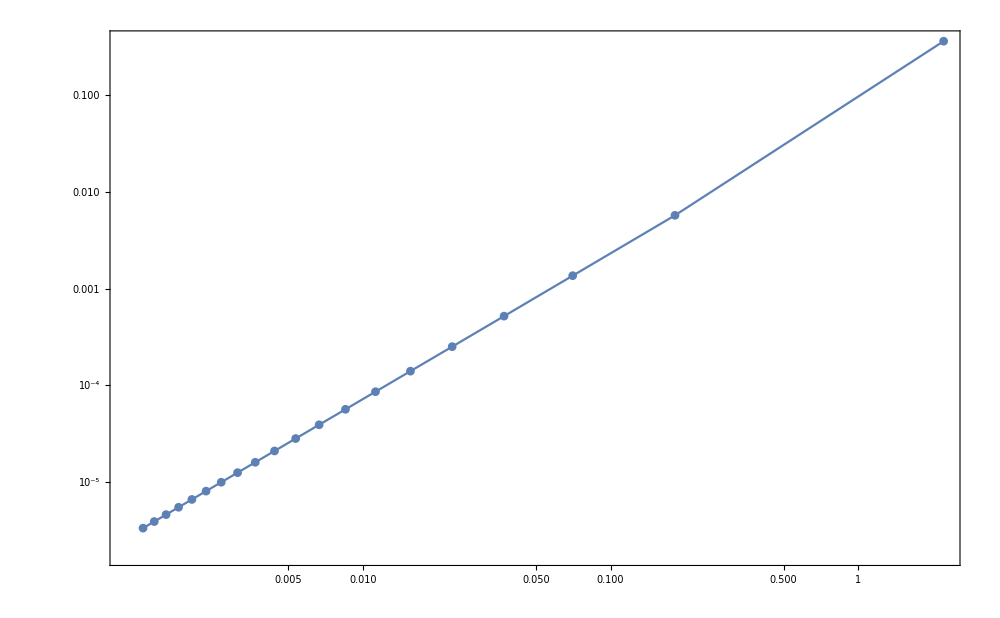

```mathematica
ListLogLogPlot[Transpose[{-enV1}~Join~{Abs@((enV1-energyVs1)/enV1)}],Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_energyVs1.mx",energyVs1];
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
Abs@(δ50V-δVs1)
```

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001592420285480551621202410579019777993933) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031971693853264036360991613869521727586065969029) is less than WorkingPrecision (50.).

End with 1.1093708s

End with 1.1093708s

{1/1000000000,-0.0010111998145828355300552285255370560006647371738294}    1.109371

{1/1000000,-0.0319608068228429445375764005083271597272872526036}    1.124995

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.899344) is less than WorkingPrecision (50.).

End with 1.2499949s

{0.001,-0.73245281260764851000775844920629134030655539829262}    1.249995

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.2275) is less than WorkingPrecision (50.).

End with 1.4374965s

{0.01,-0.88717800043865918412081518027419650034017176695375}    1.437497

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.1009510549407892795615048876387916324050937497) is less than WorkingPrecision (50.).

End with 1.0937586s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031976909397399965159177408666695726125229730203) is less than WorkingPrecision (50.).

{1/100000,-0.10061020210819769933236770725076078778315373898813}    1.093759

End with 1.1562586s

FindRoot::precw: The precision of the argument function (Tan[δ]==2271.72) is less than WorkingPrecision (50.).

{1/100000000,-0.0031976800407679159880388609962545090483672071827604}    1.156259

End with 1.1250107s

{0.003,1.570356132254887975604909374799044779675925428662}    1.125011

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.208094) is less than WorkingPrecision (50.).

End with 1.4218904s

{0.03,-0.20516608639746857401393672589441923864636073192756}    1.437514

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.01011183690340258712548932718930094677279944435) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.0781356s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31376059103807847998633417923444405432561483532) is less than WorkingPrecision (50.).

{1/10000000,-0.01011149228197983871839356667669287934155624444665}    1.078136

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0162178) is less than WorkingPrecision (50.).

End with 1.1875126s

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000,-0.30403289466906909896549077260581201179657933634888}    1.187513

End with 1.1093856s

{0.007,0.016216422618368829442322983295077716783648173005544}    1.109386

FindRoot::precw: The precision of the argument function (Tan[δ]==0.802755) is less than WorkingPrecision (50.).

End with 1.6562641s

{0.07,0.6764182979257752221650749149942871257539249908027}    1.656264

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.582471) is less than WorkingPrecision (50.).

End with 2.1250147s

{0.3,0.52743076119897135208560455523113719496774121945261}    2.140641

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.7520058243175271563404383467069708676370674012618 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.154696) is less than WorkingPrecision (50.).

End with 2.0312693s

{0.1,-0.15347975367354218123871399498421327405948098610881}    2.046895

FindRoot::precw: The precision of the argument function (Tan[δ]==6.1810138352594931227224668529308287695254464703) is less than WorkingPrecision (50.).

End with 3.5469114s

{1,1.4104003689568219732627247836931811763109578940186}    3.562535

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.05106) is less than WorkingPrecision (50.).

End with 2.8125267s

{0.7,-1.11715548423330334446975983559634204527034685129}    2.812527

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.19275579248163687281087947108921910690882555022) is less than WorkingPrecision (50.).

End with 5.2188115s

{3,-0.19042037141167716984464434588711725075622706675133}    5.234439

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.0128896086926874554344035440068081928347838485) is less than WorkingPrecision (50.).

End with 8.9844735s

{7,-1.1097134107250843884077985133813190569541841272488}    9.0157128

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.457485483385463226663113627341720189306773602) is less than WorkingPrecision (50.).

End with 7.6875835s

{10,-1.417157682919970769293364680677563052804888875311}    7.7344449

{-0.0010111998145828355300552285255370560006647371738294,-0.0031976800407679159880388609962545090483672071827604,-0.01011149228197983871839356667669287934155624444665,-0.0319608068228429445375764005083271597272872526036,-0.10061020210819769933236770725076078778315373898813,-0.30403289466906909896549077260581201179657933634888,-0.73245281260764851000775844920629134030655539829262,1.570356132254887975604909374799044779675925428662,0.016216422618368829442322983295077716783648173005544,-0.88717800043865918412081518027419650034017176695375,-0.20516608639746857401393672589441923864636073192756,0.6764182979257752221650749149942871257539249908027,-0.15347975367354218123871399498421327405948098610881,0.52743076119897135208560455523113719496774121945261,-1.11715548423330334446975983559634204527034685129,1.4104003689568219732627247836931811763109578940186,-0.19042037141167716984464434588711725075622706675133,-1.1097134107250843884077985133813190569541841272488,-1.417157682919970769293364680677563052804888875311}

{4.956147547744076993666907375123543018695×10^-13,1.7240033806538151243025229276837388589886×10^-11,5.50149105999223124751023356565140885105889×10^-10,1.741771742160420289282074444327745850782183×10^-8,5.5232890623630315872411379286083983642341508×10^-7,0.000017815167949120698360553684155201694526303152,0.0003653482973632475546431614294544719841209402003,0.000412316480712662426701218140264297270689391918,0.000387756110095462772278602673448083006397838552045,0.0004739728119128728936440891565463331654578744779,0.0021810342434727015068037715419160101496586703776,0.0052724442405842846717412402822089053114164712096,0.00730357190018487659779674823918369735939131472442,0.0235557839312956405268656890696170826424635331987,0.047895694641275631591135960993352168123035788701,0.061218276079895112515343743366316899395115150134,0.1582325465177184712230833960137109191710431466301,0.3434232510175689626018841020406929240855682544001,0.342289327201798537677934636026031987820751909546}

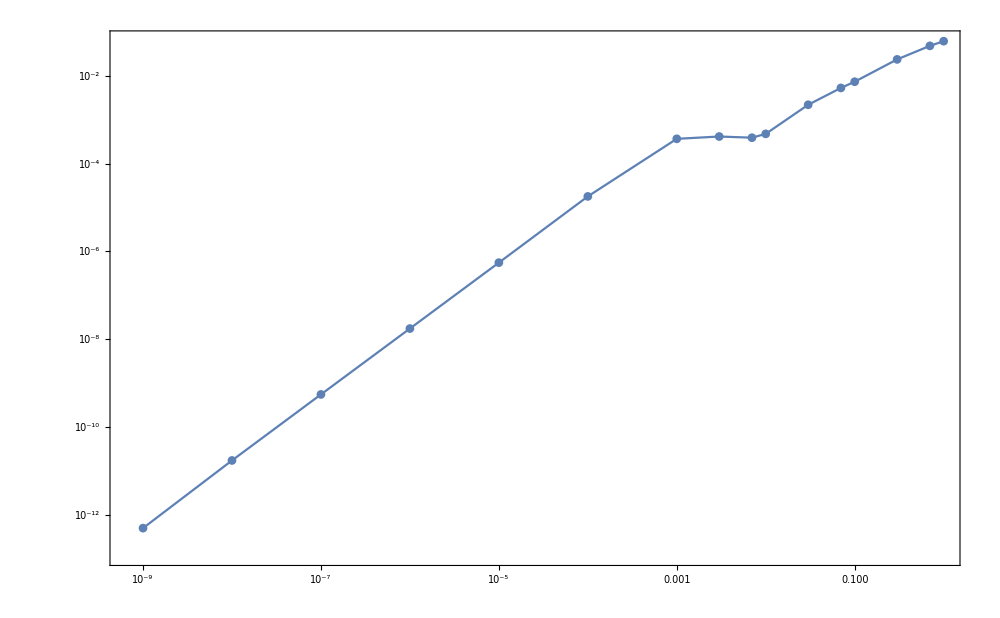

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs1)}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->1000]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
δexpminus9=δ50e[ee[[2]],V1[r,Fa]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587464132865018998597875314097697935557) is less than WorkingPrecision (50.).

End with 0.2656465s

-0.0010111998140872207752808208261703652631523828719599

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

End with 0.9836948s

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

End with 0.8716168s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.0257215s

End with 0.7815643s

End with 0.7975773s

End with 0.7855675s

End with 0.7875435s

End with 0.8145866s

End with 0.8125749s

End with 0.8636116s

End with 0.7805520s

End with 0.8516129s

End with 0.7845650s

End with 0.8476003s

{-36.2960467438514938819265262051,5.83238717691578772000732634051,0.000048419896,0.00015311719}

End with 0.7845540s

End with 0.8475978s

End with 0.7805643s

End with 0.8506014s

End with 0.8055673s

End with 0.8566052s

End with 0.8786208s

End with 0.8466089s

End with 0.8496050s

End with 0.8305881s

{-36.4745234751600742417665109283,5.31874642496672795610907338678,4.4920646×10^-6,0.00001420516}

End with 0.8586190s

End with 0.8455981s

End with 0.8656118s

End with 0.8536012s

End with 0.8516014s

End with 0.8415944s

End with 0.7095130s

End with 0.7515317s

End with 0.8897162s

End with 0.8936439s

End with 0.8636978s

End with 0.8696516s

{-36.9843693385032225023324358357,4.89142126362096524155599734732,3.509951×10^-6,0.000011099443}

End with 0.8716136s

End with 0.8706163s

End with 0.8766190s

End with 0.8716288s

End with 0.8657403s

End with 0.8596203s

End with 0.7585367s

End with 0.7815504s

End with 0.7605497s

End with 0.7845659s

{-36.9446028390687265349163285747,4.89182286431052761548226752832,3.1131044×10^-8,9.8445481×10^-8}

End with 0.7545495s

End with 0.7735599s

End with 0.7515481s

End with 0.7705522s

End with 0.7625405s

End with 0.7815639s

End with 0.8496001s

End with 0.8686145s

End with 0.7825504s

End with 0.8105723s

End with 0.8145936s

End with 0.8135754s

{-37.1800711874715597862402885555,4.69970695013297972467892467177,-2.593815×10^-8,-8.2023248×10^-8}

End with 0.7865553s

End with 0.8035659s

End with 0.7955631s

End with 0.8075720s

End with 0.8065682s

End with 0.8125844s

End with 0.8315808s

End with 0.8886405s

End with 0.7505435s

End with 0.8125684s

End with 0.8155761s

End with 0.7745592s

End with 0.7935728s

End with 0.7725590s

End with 0.8175787s

End with 0.8325887s

End with 0.8105699s

End with 0.8756316s

End with 0.7835666s

End with 0.7695431s

End with 0.7885588s

End with 0.7855532s

{-37.1869576573549728246442839686,4.69411914182335661765633556905,-2.5902834×10^-8,-8.1911572×10^-8}

End with 0.7935729s

End with 0.7635393s

End with 0.8175729s

End with 0.7815639s

End with 0.7945733s

End with 0.7716496s

End with 0.7335329s

End with 0.6604750s

End with 0.7795634s

End with 0.8155872s

End with 0.7985642s

End with 0.7895609s

End with 0.7875596s

End with 0.7705461s

End with 0.7995627s

End with 0.7445384s

End with 0.7645406s

End with 0.7575477s

End with 0.8536046s

End with 0.8396045s

End with 0.8716291s

End with 0.8776322s

{-37.1939142379074901152003462084,4.68847529004580597665505941648,-2.5868556×10^-8,-8.1803174×10^-8}

End with 0.8616208s

End with 0.8646113s

End with 0.8626222s

End with 0.8506010s

End with 0.8536173s

End with 0.8506137s

End with 0.7881664s

End with 0.7515316s

End with 0.8616086s

End with 0.8736175s

End with 0.8045795s

End with 0.7991169s

End with 0.8246352s

End with 0.8145710s

End with 0.8065711s

End with 0.8145735s

End with 0.8326006s

End with 0.8356033s

End with 0.7505303s

End with 0.7585479s

End with 0.7455204s

End with 0.7441414s

{-37.2007793396540431745328232243,4.68290651489019381527430673703,-2.5833155×10^-8,-8.1691229×10^-8}

End with 0.7475304s

End with 0.7425251s

End with 0.7405216s

End with 0.7515304s

End with 0.7635512s

End with 0.7365332s

End with 0.8415940s

End with 0.9486690s

End with 0.9616813s

End with 0.9356600s

End with 1.1027799s

End with 0.9216505s

End with 0.8475982s

End with 0.8405940s

End with 0.7885568s

End with 0.8055689s

End with 0.8215815s

End with 0.8035655s

End with 0.8065699s

End with 0.8796217s

End with 0.7975649s

End with 0.8776223s

{-37.2076810254911364504933332345,4.67730890303732209340705729218,-2.5798341×10^-8,-8.158114×10^-8}

End with 0.8686153s

End with 0.8255818s

End with 0.7705445s

End with 0.8335904s

End with 0.8005661s

End with 0.8135759s

End with 0.8305860s

End with 0.8175758s

End with 0.7655399s

End with 0.7815516s

End with 0.8255827s

End with 0.9136470s

End with 0.7925468s

End with 0.7815536s

End with 0.8025675s

End with 0.7365086s

End with 0.9036395s

End with 0.8035692s

End with 0.8105727s

End with 0.8405939s

End with 0.8255840s

End with 0.8045693s

End with 0.8726169s

End with 0.7685410s

{-37.2123935219386110390323171683,4.67348727558430569249019177476,-2.5779435×10^-8,-8.1521353×10^-8}

End with 0.9107062s

End with 0.7980642s

End with 0.8891299s

End with 0.8015998s

End with 0.8445975s

End with 0.7655424s

End with 0.9136453s

End with 0.9516741s

End with 0.9276568s

End with 0.9676834s

{-37.2116958994458717956512139856,4.67429117410172459642392321806,6.1583733×10^-13,2.3480253×10^-12}

End with 0.9546749s

End with 0.9566746s

End with 0.9166460s

End with 0.9216506s

End with 0.9116443s

End with 0.9396640s

End with 0.9376622s

End with 1.0347302s

End with 0.9306563s

End with 1.0407348s

{-37.2117467651313705412034906459,4.67424991790377539922785500836,-4.299018×10^-15,3.8697217×10^-13}

End with 0.9866958s

End with 1.0597472s

End with 0.9046404s

End with 1.0247243s

End with 0.9766917s

End with 1.0547443s

End with 0.7955631s

End with 0.8105723s

End with 0.8165782s

End with 0.7841167s

End with 0.9016372s

End with 0.8661102s

End with 0.7885584s

End with 0.7295149s

End with 0.8005665s

End with 0.7945573s

End with 0.7935621s

End with 0.8301308s

End with 0.9816925s

End with 0.8736170s

End with 0.9937002s

End with 0.9856978s

End with 0.8956326s

End with 0.8241995s

End with 0.8626090s

End with 0.9136462s

End with 0.9466692s

End with 1.0027059s

End with 0.9392806s

End with 0.9646832s

{-37.2121505125253527801144873917,4.67392249166173220214785437282,-1.6143622×10^-13,-1.1001297×10^-13}

End with 0.9636802s

End with 0.9486702s

End with 0.9526734s

End with 1.0327275s

End with 0.9486698s

End with 0.9876980s

End with 0.9586773s

End with 1.0177298s

End with 0.9676719s

End with 1.0007070s

End with 0.9987056s

End with 1.0227221s

{-37.2121430104622537728499902907,4.67392857583323010404114302465,-1.2989479×10^-13,-1.0268812×10^-14}

End with 0.9536727s

End with 1.0197222s

End with 0.9506712s

End with 1.0227229s

End with 0.9546769s

End with 1.0277230s

End with 0.9176465s

End with 0.9286556s

End with 0.9997081s

End with 0.9562756s

{-37.2121014362598278920470775094,4.67396229092024646394797470813,-1.2831535×10^-13,-5.2666223×10^-15}

End with 0.9486719s

End with 0.9286556s

End with 1.0177192s

End with 0.9196610s

End with 0.9196348s

End with 1.0207232s

End with 0.9276548s

End with 0.9306591s

End with 0.9336528s

End with 0.9726851s

End with 1.0127125s

End with 1.0547443s

End with 1.1247934s

End with 1.0547472s

End with 1.1538161s

End with 1.1077832s

End with 1.0857705s

End with 1.1528147s

End with 1.1338016s

End with 1.1127853s

End with 1.0747609s

End with 1.1107850s

End with 1.1518155s

End with 1.0547426s

End with 1.1448087s

End with 1.1187899s

End with 1.1327970s

End with 1.0917764s

End with 1.0607498s

End with 1.1057793s

End with 1.1658233s

End with 1.0627516s

End with 1.0747609s

End with 1.0947738s

End with 1.0487413s

End with 1.0967583s

End with 1.1157885s

End with 1.1398054s

End with 1.0887724s

End with 1.1147875s

End with 1.0507448s

End with 1.0977737s

{-37.2121014648333776771116544368,4.67396226774819063352402207675,-1.2831535×10^-13,-5.2666256×10^-15}

End with 1.0857660s

End with 1.0797638s

End with 1.0827645s

End with 1.0777620s

End with 1.0847659s

End with 1.0867653s

End with 1.1057818s

End with 1.0477420s

End with 1.1708291s

End with 1.1217907s

End with 1.1878385s

End with 1.2108561s

End with 1.0697543s

End with 1.0837687s

End with 1.1768326s

End with 1.2218638s

End with 1.1137866s

End with 1.1137870s

End with 1.0807619s

End with 1.0717552s

End with 1.0437379s

End with 1.0757606s

{-37.212099223101870382281335503,4.67396408570673510769114964292,-1.2831513×10^-13,-5.2655061×10^-15}

End with 1.0667545s

End with 1.0157087s

End with 1.0607473s

End with 1.0857664s

End with 1.0427383s

End with 1.0997767s

End with 1.1257926s

End with 1.1898411s

End with 1.0577454s

End with 1.0697547s

End with 1.0357311s

End with 1.0937737s

{-37.212100216338237988712508461,4.67396328034960778671055775111,-1.153674×10^-13,3.5678616×10^-14}

End with 1.0617548s

End with 1.1428064s

End with 1.0667536s

End with 1.0887646s

End with 1.0607497s

End with 1.0917731s

End with 0.9957040s

End with 1.0017067s

End with 1.1177952s

End with 1.1488099s

End with 1.1378043s

End with 1.0797618s

End with 1.0497422s

End with 1.1247934s

End with 1.2979174s

End with 1.1668246s

End with 1.1578197s

End with 1.1328031s

End with 1.1618226s

End with 1.1297967s

End with 1.0717565s

End with 1.0877682s

End with 1.0757618s

End with 1.1147862s

End with 1.0877699s

End with 1.0977761s

End with 1.1358042s

End with 1.1277949s

End with 1.1628231s

End with 1.1097817s

End with 1.2058504s

End with 1.1538165s

End with 1.2048458s

End with 1.1598113s

End with 1.1618205s

End with 1.1358038s

End with 1.1978451s

End with 1.1528160s

End with 1.0587491s

End with 1.1297999s

End with 1.0517444s

End with 0.9967037s

End with 0.9196512s

End with 1.0162761s

End with 0.9166493s

End with 0.9756879s

End with 0.9452093s

End with 0.9532371s

End with 0.9146466s

End with 0.9622244s

End with 0.9106417s

End with 0.9606778s

End with 0.8826191s

End with 0.9126440s

End with 0.9026352s

End with 0.9676839s

End with 0.8666106s

End with 0.9516722s

End with 0.8736179s

End with 0.9346607s

End with 0.8886283s

End with 0.9486702s

End with 0.8956326s

End with 0.9246512s

End with 0.8736170s

End with 0.9076407s

End with 0.8842732s

End with 0.9671826s

End with 0.9021361s

End with 0.9606779s

End with 0.9121427s

End with 0.9431660s

End with 0.8916302s

End with 0.9452052s

End with 0.8756189s

End with 0.9406646s

End with 0.8916297s

End with 0.9406646s

End with 0.8836241s

End with 0.9366610s

End with 0.8806218s

End with 0.9296549s

End with 0.8706163s

End with 0.9196496s

End with 0.8736170s

End with 0.9436641s

End with 0.8836171s

End with 0.9056405s

End with 0.8666127s

End with 0.9276556s

End with 0.8996354s

End with 0.9477247s

End with 0.9156475s

End with 0.9502303s

End with 0.9026377s

End with 0.9236499s

End with 0.9166489s

End with 0.9096297s

End with 0.8686133s

End with 0.9336582s

End with 0.8986464s

End with 0.9256538s

End with 0.9366614s

End with 0.9546753s

End with 0.9947023s

End with 0.9296538s

End with 0.8736170s

End with 0.9516718s

End with 0.8826244s

End with 0.9432325s

End with 0.9486842s

End with 0.9871946s

End with 0.8966807s

End with 0.9056413s

End with 0.8766194s

End with 0.9292305s

End with 0.9467135s

End with 0.9466700s

End with 0.8736171s

End with 0.9326700s

End with 0.8686121s

End with 0.9186470s

End with 0.9066389s

End with 0.9256538s

End with 0.8616085s

End with 0.9236511s

End with 0.9006359s

End with 0.9386611s

End with 0.9226514s

End with 0.9136437s

End with 0.8721654s

End with 0.9271568s

End with 0.9066516s

End with 0.9336599s

End with 0.8901292s

End with 0.9512284s

End with 0.8916199s

End with 0.9386607s

End with 0.9616796s

End with 0.9636794s

End with 0.8996395s

End with 0.9336590s

End with 0.8856251s

End with 0.9766884s

End with 0.9406658s

End with 0.9466692s

End with 0.9036395s

End with 0.9326462s

End with 0.8856230s

End with 0.9636819s

End with 0.8926303s

End with 0.9356608s

End with 0.9186498s

End with 0.9776905s

End with 0.8796205s

End with 0.9586781s

End with 0.9056409s

End with 0.9532502s

End with 0.9171428s

End with 0.9837884s

End with 0.9526743s

End with 0.9556771s

End with 0.8986337s

End with 0.9196499s

End with 0.8946304s

End with 0.9536752s

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-37.2121002163382379887125084611,4.673963280349607786710557751}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_c2d1.mx",{c2,d1}];
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.56857,-0.181026,-0.0702548,-0.0371286,-0.022921,-0.0155471,-0.0112345,-0.00849604,-0.00664931,-0.00534528,-0.00439039,-0.00367028,-0.00311383,-0.00267497,-0.00232275,-0.00203578,-0.00179888,-0.00160105,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$13784]-u''[r$13784]/2==e$13783 u[r$13784],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.5685748631682357783135750207,-0.181026486502200639496571132582,-0.070254830674820536213199127543,-0.0371286504340277450018934854778,-0.0229209806930553394506359970815,-0.0155471285731899931056933177378,-0.0112344870402446657082844890104,-0.00849604147684492760940495784873,-0.00664930878714140590975166624439,-0.00534528135305987770883163026748,-0.00439039502315246600456786479796,-0.00367027996033754989959631052105,-0.0031138343104567922694241488144,-0.00267496954903121954591652151628,-0.00232274818836380907089365305896,-0.00203577720433811209940786580856,-0.00179888076727626922778443801348,-0.00160105161240657339489155051192,-0.00143414881331963196920371232907,-0.00129204659152907310452860120281}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_energyVs2.mx",energyVs2];
```

```mathematica
Abs@((energyVs2-enV1)/enV1)
```

{0.29276573923810897831836841572,0.00644635111339896390456881169,0.0012514656093235780854532013,0.00044972607668042328686448718,0.00021195801898722899045310064,0.0001166527606369953794013243,0.00007103326736112262736485481,0.00004645725013289382597842545,0.00003204599745131279693076525,0.00002303679817915729709358097,0.0000171153342999491747225818,0.0000130631669855103805935118,0.0000101966179540688728100557,8.11161654290980903795645×10^-6,6.55880149587024108810135×10^-6,5.37855897758955680464633×10^-6,4.46547054946766507906029×10^-6,3.74799441940530252881754×10^-6,3.17641023510660429143138×10^-6,2.71542947666949314544283×10^-6}

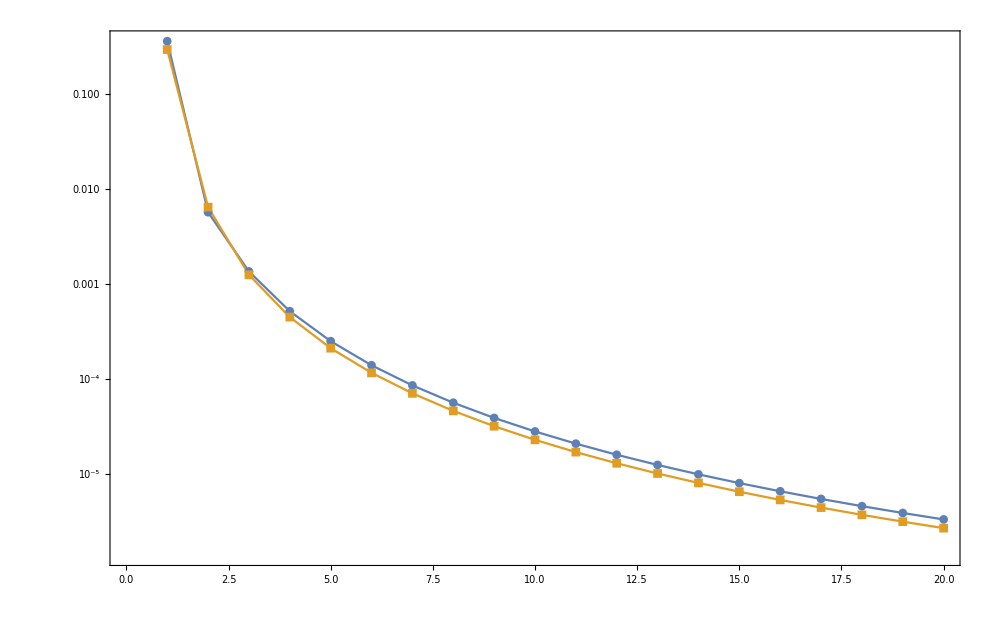

```mathematica
ListLogPlot[{Abs@((energyVs1-enV1)/enV1),Abs@((energyVs2-enV1)/enV1)},Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
Module[{eeee,timea,timeb},
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-7.72293005383498],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
timeb=SessionTime[];
Print[{eeee},"    end with ",timeb-timea,"s"];
eeee
]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.7520058243175271563404383467069708676370674012618 Power[«2»]-Power[«2»] Erf[«1»]) u[r$167868]-u''[r$167868]/2==e$167867 u[r$167868],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

$Aborted

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
Abs[If[Abs@#>π/2,#-π,#]&/@(δ50V-δVs2)]
```

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898151) is less than WorkingPrecision (50.).

End with 0.9687479s

{0.001,-0.73179278880247803277373717810593037399205178519765}    0.9687479

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031971662339799414250976363792362528125776239451) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.0312479s

{1/1000000,-0.03196077534155812030543690759170403466202103700542}    1.046873

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22537) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112001587107346343220892957555530244803859291) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.1718782s

End with 1.2031241s

{0.01,-0.88632844902075763273864588992436151067558470750521}    1.171878

{1/1000000000,-0.0010111998140515421595833139301110463900512004473604}    1.203124

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095004614393458749224222481409001532596223462) is less than WorkingPrecision (50.).

End with 1.0000214s

FindRoot::precw: The precision of the argument function (Tan[δ]==-3298.1) is less than WorkingPrecision (50.).

{1/100000,-0.10060920348829210125542857136562568385439587880279}    1.015648

End with 1.1406352s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.003,-1.570493122134603966522547234727337421047296882468}    1.140635

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031976909097217943529632640296535927174972363459) is less than WorkingPrecision (50.).

End with 1.1875110s

{1/100000000,-0.003197680010750020764884610792688824424321630318304}    1.203136

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.204089) is less than WorkingPrecision (50.).

End with 1.5000096s

{0.03,-0.20132395635230140758999631172595462164243692256631}    1.515635

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31372521088456863230932483429745985732258214253) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9531201s

{1/10000,-0.30400068505617715310179802785717110827431903981791}    0.9531201

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0169148) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.1562627s

{0.007,0.016913140696428054131756604325644369547610871597572}    1.171887

NDSolve::precw: The precision of the differential equation ({{2 (1+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010111835912229271256298825996771950780979120015) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.0156348s

{1/10000000,-0.010111491290907859201472231066301311241112268624135}    1.03126

NDSolve::precw: The precision of the differential equation ({{2 (7+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.817653) is less than WorkingPrecision (50.).

End with 1.8125297s

{0.07,0.68541257489156634116671649891186719355311912173879}    1.828145

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.628865) is less than WorkingPrecision (50.).

End with 1.8281423s

{0.3,0.5613735917554611543194041428815469072738319115013}    1.843768

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.142266) is less than WorkingPrecision (50.).

End with 2.1093943s

{0.1,-0.14131771447066474206464904505955537550672834884766}    2.109394

FindRoot::precw: The precision of the argument function (Tan[δ]==9.890117752216530704731654824502344302169818408) is less than WorkingPrecision (50.).

End with 3.5000339s

{1,1.470027765311698479213372543839764585276333133455}    3.515662

NDSolve::precw: The precision of the differential equation ({{2 (3+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.79589) is less than WorkingPrecision (50.).

End with 2.5781666s

{0.7,-1.0627258457819602725541680025941605982478867405351}    2.578167

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.12966673398873412528298302598744039619803893761) is less than WorkingPrecision (50.).

End with 4.5469166s

{3,-0.12894726267869570384775815630472848843178285472457}    4.562539

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.7744548628128403581877229653322394118059820057) is less than WorkingPrecision (50.).

End with 8.3594668s

{7,-1.0576070481825940999279288350786176387996575870842}    8.3907045

NDSolve::precw: The precision of the differential equation ({{2 (10+2.36273154348466971327529407204 Power[«2»]-4.673963280349607786710557751 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.919988278562857601804707077667549652554346374) is less than WorkingPrecision (50.).

End with 7.9688424s

{10,-1.3702753120981237299336261712222031547889700461436}    8.0000804

{-0.0010111998140515421595833139301110463900512004473604,-0.003197680010750020764884610792688824424321630318304,-0.010111491290907859201472231066301311241112268624135,-0.03196077534155812030543690759170403466202103700542,-0.10060920348829210125542857136562568385439587880279,-0.30400068505617715310179802785717110827431903981791,-0.73179278880247803277373717810593037399205178519765,-1.570493122134603966522547234727337421047296882468,0.016913140696428054131756604325644369547610871597572,-0.88632844902075763273864588992436151067558470750521,-0.20132395635230140758999631172595462164243692256631,0.68541257489156634116671649891186719355311912173879,-0.14131771447066474206464904505955537550672834884766,0.5613735917554611543194041428815469072738319115013,-1.0627258457819602725541680025941605982478867405351,1.470027765311698479213372543839764585276333133455,-0.12894726267869570384775815630472848843178285472457,-1.0576070481825940999279288350786176387996575870842,-1.3702753120981237299336261712222031547889700461436}

{3.56786156975068960593188731011824245994×10^-14,1.2777861416616098960540455347208188274571×10^-11,4.40922873517698210859368211535303090716626×10^-10,1.406356740262793660009587868178780770777635×10^-8,4.4629099936177378041177134224308892143677026×10^-7,0.0000143944449428251653321910644857018277339933789,0.0002946755078072296793781096709064943303826728947,0.000331082719588633908485555612856386203257696327,0.00030896196796376191715501835711856975756486003998,0.0003755786059886784885252011932886564991291849707,0.0016610958016944649171366426265486068542651389836,0.0037218327252068343299003436353711624877776597265,0.00485846730269256257626820168547420119336132253673,0.01038704662519416170693389858079262966362715885,0.0065339438100674403244558720088292788994243220539,0.0015908797250186065646959832197334904297399107,0.09675943778473700522619720643132215684659893460332,0.2913168884750786741220144237379915059310417142355,0.2954069563799514983181961265706720898048330803785}

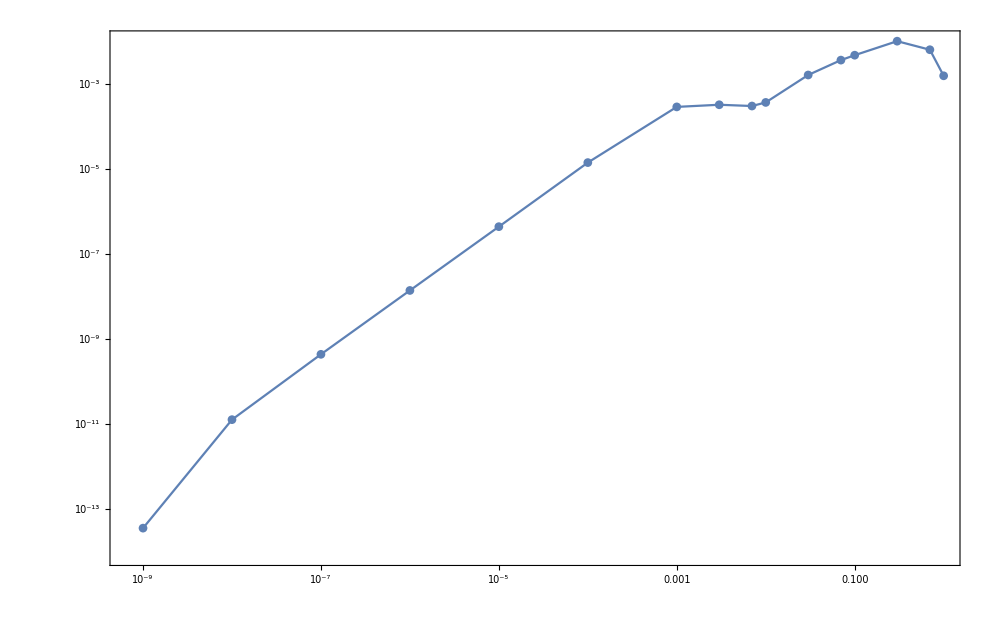

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs[If[Abs@#>π/2,#-π,#]&/@(δ50V-δVs2)]}],Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_energyVs1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_c1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_energyVs2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_c2d1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_efV1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_efVs2.mx"]
```

```mathematica
nRange=20;
```

```mathematica
AbsoluteTiming[efV1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[PrintTemporary[n];
efunction[[n]]=First@Eigenfunsin[V1[r,Fa],enV1[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.01},{Exclusions->1}];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

1

4

7

10

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-2.2178999946615110039963719593 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0371453556690997081330810405359 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0112352851192564202921100218141 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00534540449406439343068311389881 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

11

5

8

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00439047016751711701387966530571 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0229258400086871989459936271472 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00849643619790661193026557657521 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

2

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.182201018238987964491115076648 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

12

6

9

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00367032790644388335476624096803 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0155489424002459674269360739472 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00664952187770255121439165323797 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

3

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0703428623479103283909200952531 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

13

15

17

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.0031138660613593800922055490907 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00232276342290802179270840312092 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00179888880016122811497251004208 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

14

19

16

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00267499124753447518551336507628 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00143415336877907127166205711352 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00203578815394476396948883502542 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

18

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00160105761316157267083956547849 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

20

NDSolve::precw: The precision of the differential equation ({{f[r] (-Power[«2»]+If[«5»,-2.7156298495422798770722075365871798715065108699048,0])-f''[r]/2==-0.00129205009999999997829482778267 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1740.9,{2.62312706066×10^-1782                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.23843451004×10^-471                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],8.19527×10^-270                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.24029×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],5.00942×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.48263×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.3071×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.40678×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.90957×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.08994×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79562×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.000015699                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.5802                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.9282×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.13749×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.88869×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186006                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2851.66                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28857×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.38815×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

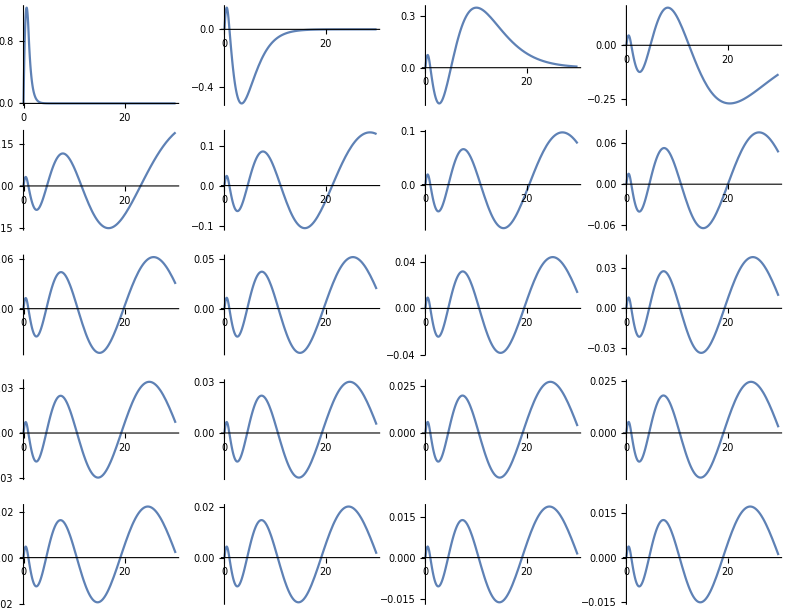

```mathematica
GraphicsGrid@Partition[Table[Plot[efV1[[n]],{r,0,30},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full],{n,1,20}],4]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_efV1.mx",efV1];
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.5685748631682357783135750207 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371286504340277450018934854778 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112344870402446657082844890104 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534528135305987770883163026748 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439039502315246600456786479796 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229209806930553394506359970815 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849604147684492760940495784873 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.181026486502200639496571132582 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367027996033754989959631052105 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155471285731899931056933177378 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664930878714140590975166624439 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.070254830674820536213199127543 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0031138343104567922694241488144 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232274818836380907089365305896 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179888076727626922778443801348 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414881331963196920371232907 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267496954903121954591652151628 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577720433811209940786580856 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160105161240657339489155051192 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.36273154348466971327529407204 Power[«2»]+4.673963280349607786710557751 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129204659152907310452860120281 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1632.21,{3.07649084661×10^-1490                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.65158804703×10^-469                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.31498×10^-269                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.40731×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],5.25232×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.51522×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.35652×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.46886×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.91735×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.10614×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79888×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000157191                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.6642                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.93117×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.14376×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.89041×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186093                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2852.71                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28896×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.39021×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

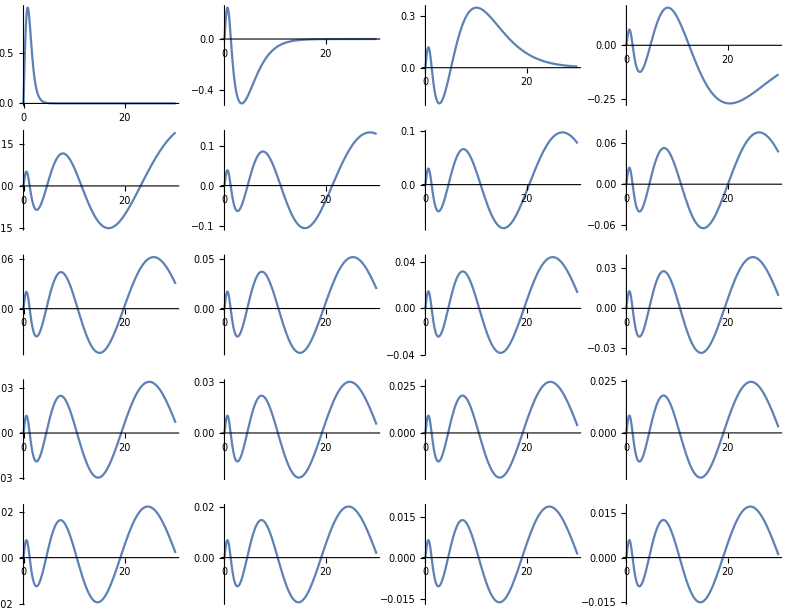

```mathematica
GraphicsGrid@Partition[Table[Plot[efVs2[[n]],{r,0,30},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full],{n,1,20}],4]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_efVs2.mx",efVs2];
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,If[n>15,4000,b]},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,If[n>15,4000,b]},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
REAL=NIntegrate[D[efV1,{r,2}]^2,{r,0,2000},Exclusions->1,WorkingPrecision->30,PrecisionGoal->10];
N[%,6]
REF=NIntegrate[D[Take[efV1,-3],{r,2}]^2,{r,0,2000},Exclusions->1,{MaxRecursion->30,WorkingPrecision->30,PrecisionGoal->10}];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (6.8807955764×10^-3564 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (2.74411961159×10^-941 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (6.71624485020171×10^-539 («1»)^2) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{39.6525,1.53907,0.412472,0.16554,0.0822261,0.0466223,0.0289309,0.0191673,0.0133454,0.00966111,0.00721705,0.00553241,0.00433375,0.00345775,0.00280277,0.00230329,0.00191577,0.00161051,0.00136681,0.0011699}

NIntegrate::precw: The precision of the argument function (8.13197×10^6 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},«39»,{46,45},{47,46},{48,47},{49,48},{50,49},«11495»},{«1»}}}][r])^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (1.66041×10^16 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},«39»,{46,45},{47,46},{48,47},{49,48},{50,49},«10778»},{«1»}}}][r])^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (4.08084×10^-15 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,4000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},«38»,{46,45},{47,46},{48,47},{49,48},{50,49},«11515»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.00161051,0.00136681,0.0011699}

### Matrix element in V_eff^(a^2)

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

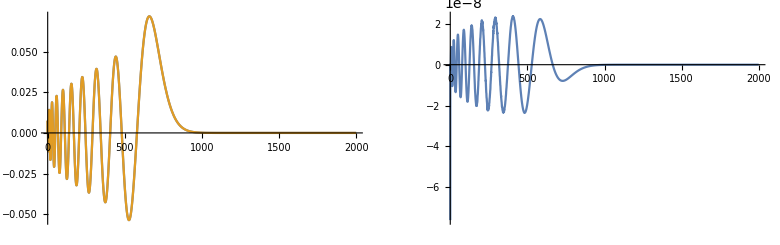
{316.214,-Graphics-}

```mathematica
AbsoluteTiming@Module[{n=19},ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium]}}
]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]
Abs@((%-REAL[[20]])/REAL[[20]])
```

0.00103203

0.0517522

```mathematica
AbsoluteTiming[efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243863935055737602971 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00312500761726746385913647922606 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040862718159308244150419666 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00050000007796292676973750649047 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223188903938793994512264818 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000781250237936304904722289140259 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00200000249550536888652531039438 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222253552894523182159148667 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617284082651037569419393087846 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00138888989166308326560993291706 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000295858009162576239009167422901 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000222222232488422260934584517289 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000255102055311667723228331312929 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0125002441801421361773951351802 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000195312507434709104520394621199 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918009791462567717346 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000154320991780025227507069598258 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000125000002436179368929957388996 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{2445.63,{8.41457014008×10^-818                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.480197172726×10^-380                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],8.39339×10^-233                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.14087×10^-158                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],3.44212×10^-113                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.2177×10^-82                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.63894×10^-60                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.11706×10^-43                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.11448×10^-30                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.23154×10^-19                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.02554×10^-10                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.00340555                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],9183.21                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-3.3482×10^9                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.39999×10^14                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.12086×10^-31                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],4.58687×10^-24                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1.70214×10^-17                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1.40823×10^-11                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-3.21204×10^-6                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
Module[{n=14,efunction},
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]]
]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx",efVs1];
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,If[#>15,4000,2000]},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4623668815636586952048333778507701378928326188347611607266528355568406087082334849813321133116737352}. NIntegrate obtained 4.24775143448205958754880454950146237906635095041566811870478274004760680511885743899799314631144069 and 9.4294993357277365201116231630111112705893449190092986268406862750987694486421162445050224791268157×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4659802004911373337071412325364140666142675879536833723647658789795401373362383226469339285990687524}. NIntegrate obtained 0.7174212809199777929012894664292984532181745825076807971498109279693081909549759755618068069181562719 and 3.633547634066690580084017448059494709124396188637866489408592955265507683293373880163695855550865649×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.04490049372286×10^-465 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4876851693547784171767109075724296318712432966469218138641756757990863061327905245533927872319965803}. NIntegrate obtained 0.2310293704005218476208680659105967534842423940550152647074475234522278493705018614045060625254064782 and 1.565100318490618058414719654037227888225773080342227279351087081435626816539107499249587825522316916×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01984903187431712853938055156973597616852240651017562336163919592199692943063748185718615390076255168 and 2.074762998997241455182522314947624539621804802400464589855355901814498606670080863891670931669490639×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0134018318956914725368765651229453202777814174071243471793431669035110112443153993803885775000156491 and 1.349272075646587028220132847748484682868033567759296291558026803594026509245122889347926101283489337×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.009469642671235533884112092422123566763653524626848019889082198752430783453376630716086874204278076897 and 9.499293015886584565705581065264491615077331817953452020612324005259862951024457468747029254543415047×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{4.24775,0.717421,0.231029,0.101363,0.053096,0.0311892,0.019849,0.0134018,0.00946964,0.00693668,0.00523211,0.0040432,0.00318883,0.00255916,0.00208492,0.00172097,0.00143703,0.00121227,0.00103203,0.000885825}

{0.15045,0.11702,0.108887,0.105207,0.103108,0.101751,0.100801,0.1001,0.0995605,0.0991327,0.0987853,0.0984974,0.098255,0.098048,0.0978694,0.0977135,0.0975763,0.0974547,0.0973461,0.0972486}

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,If[#>15,4000,2000]][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{(*15,*)20})==(REF[[#]]&/@{(*2,*)3})](*/.Z->1*),{γ,-1,-10},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10,MaxIterations->10000]
((p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{15,20})-(REF[[#]]&/@{2,3}))/(REF[[#]]&/@{2,3})/.RESVs1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

FindRoot::precw: The precision of the argument function ({0.000885825+0.000282618 γ==157/160000}) is less than WorkingPrecision (50.).

{γ→0.33764725954412159015702246610372791534324179410807}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

{1.02139,9.66804×10^-17}

```mathematica
p4Vs1=p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.558842}. NIntegrate obtained 0.00838342 and 0.0000125049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00172097 and 3.23177×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00143703 and 2.82697×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5.01942,0.813096,0.259336,0.113299,0.0592056,0.0347244,0.0220751,0.0148931,0.0105169,0.00770014,0.00580569,0.004485,0.00353632,0.00283738,0.00231112,0.00190735,0.00159242,0.00134317,0.00114333,0.00098125}

{0.00388414,0.000734028,0.000295047,0.000156002,0.0000949686,0.0000629033,0.0000440104,0.0000319552,0.0000237978,0.0000180236,0.0000137876,0.0000105888,8.11453×10^-6,6.20316×10^-6,4.50098×10^-6,3.31483×10^-6,2.25921×10^-6,1.37747×10^-6,6.32936×10^-7,0.}

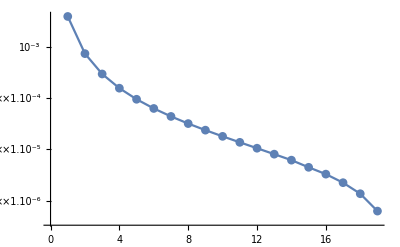

```mathematica
ListLogPlot[%161,Joined->True,PlotMarkers->{Automatic}]
```

### Matrix element in V_eff^(a^4)

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->30,PrecisionGoal->10}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs2)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (9.46479592925×10^-2980 («1»)^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (7.03091917115×10^-938 («1»)^2) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (1.72916026534559×10^-538 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{44},{45},{46},{47},{48},{49},«14377»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{6.80860718153090319522281436157,1.6941032253182392659326834256,0.4469143050800457247135553039,0.177921450733207258280947782298,0.0880224624318954812444954966972,0.0497952938377496117717358731952,0.0308556452879940534378251631071,0.0204226859967967058930375505246,0.0142096115121536027981492345565,0.0102814676544099010594729433459,0.00767743967099454487906279311923,0.00588348804249190454989655261135,0.0046075966696603248994226531056,0.00367548446740187905296370809672,0.00297874682271866686404965832948,0.00244754264467723000615953050569,0.00203549329018730753544420029826,0.00171097864017348615332345226592,0.00145193614517041855932958815708,0.00124265336200958910537645207564}

{6.80861,1.6941,0.446914,0.177921,0.0880225,0.0497953,0.0308556,0.0204227,0.0142096,0.0102815,0.00767744,0.00588349,0.0046076,0.00367548,0.00297875,0.00244754,0.00203549,0.00171098,0.00145194,0.00124265}

{0.828293,0.100728,0.0835029,0.0747919,0.0704932,0.068057,0.0665284,0.0654961,0.0647598,0.0642123,0.0637913,0.0634589,0.0631905,0.0629698,0.0627855,0.0626295,0.0624958,0.0623802,0.0622793,0.0621904}

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{18,19,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,0.9,1.1},{γ,-0.,-1},{η,-0.,-1}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

NIntegrate::precw: The precision of the argument function (8.13797×10^6 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«4»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00171097864017347981160865681594299602116505602370150196331596347105871290800001089492589651928075938 and 7.464413944320388005941854078182164492831733644890438794440921030695006587728353073925123202492441525×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (516709. ⅇ^(-r^2/2) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},«31»,{41},{42},{43},{44},{45},{46},{47},{48},{49},«11294»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5964656953800189736755032798150367690487635239523475210783961970155537389623889425112088619230236071}. NIntegrate obtained 2.332058934890988159253047978027214115363370560678346394099103611695320443393660611247036884064810644×10^-6 and 8.229285013376811972265577583728361463036881422585610173808511864903964475047252835929519138761731407×10^-29 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (8.13797×10^6 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«4»][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5964655912542165843920490337660675928463997175181554331218098108497346569002013496073756565033336758}. NIntegrate obtained -2.872311093201310944410109982107930387670261149499450714795018995610006458072664438152951300663214847×10^-6 and 1.526637362674591039395656554543954134914030507320453250968017099699731784662024330817660118391290427×10^-28 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001451936145170393833567709995136800476544113267679976567013009441961878431869771439450249920298195909 and 1.504099843779144259262415071501742098971824869642739736294693969188544915466094096725345337109324055×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.6724641841994343075714597607692690705993235200100502961113598723709447953313794437224994111131992665}. NIntegrate obtained 1.976955986350269862210879665289037079406903289163970765277605379349867052021919720151240035203916019×10^-6 and 1.62091376668808365340131583919807175072219046901327241039376560995581974751009747117610016519485906×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ({0.0017109786401734798116086568159429960211650560237015 Z+2.3320589348909881592530479780272141153633705606783×10^-6 γ-2.8723110932013109444101099821079303876702611494995×10^-6 η==0.00161051441082978095927206041699,«1»,0.0012426533620095852735800819125739453842837475953737 Z+«81» γ-2.0825287850610879168078117259003916985187600982866×10^-6 η==«64»}) is less than WorkingPrecision (50.).

{Z→1.0016359131623329273745522430442077719086462767414,γ→-210.23138043233540424487043950472739204481250837637,η→-134.7377476715893141037945561570355686922470709921}

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (9.46479592925×10^-2980 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.327670797499320919669620521954185023213924802392059610167146639518620017835176704128752146176407362}. NIntegrate obtained 6.808607181530924683854428529178380438603470032246217436240574155558262278163341800835124647094879017 and 6.914683235343655041308182024467460628366173591346840231956072076632546356565231280901660326603164469×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (6.00954306924×10^-2981 ⅇ^(-r^2/2) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{44},{45},{46},{47},{48},{49},«59954»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.327670947558574074150630199454424419390862942487354005558693471180340890991272689191134694257986506}. NIntegrate obtained 0.03870280530644742729984346515628106744715284447825218753371999763597005651686100277810042886663216726 and 7.434824301838806984506711057583091448336839867459201526488378739535970262161376213652239427990380503×10^-25 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (9.46479592925×10^-2980 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.327670947558574074150630199454424419390862942487354005558693471180340890991272689191134694257986506}. NIntegrate obtained -0.0846072394239743031410119412402517202025216912284305143717487917276394294576702668935561472783534364 and 9.985223566236852088735853329648740034420146211576603454429579397670834748258071438184479419521291829×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.694103225318246651239734892265536806675999297890047017687280547489422298818852249832048710441672919 and 4.451370058325672191187555212038168227583204422718329090976594634768004691641604655060121583001634369×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.4469143050800455772426334136276507686911244120791089217121909380721624821691511111476574385278770522 and 1.19734990768179181678584268167917883065154485540060607196186021066079657730934400886569120419609758×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08802246243189551360297972067720566064206351741366798933032177429450934128234649316156939215158164391 and 5.965967999177555987096999813051235061562266760421206596694423997881975979923135060105030581044189164×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{10.083,1.49187,0.410797,0.165363,0.0821948,0.0466149,0.0289288,0.0191666,0.0133451,0.00966102,0.00721702,0.00553239,0.00433374,0.00345775,0.00280277,0.00230329,0.00191577,0.00161051,0.00136681,0.0011699}

{0.745716,0.0306723,0.00406042,0.00106895,0.00038015,0.000159116,0.0000733855,0.000035908,0.0000181771,9.3384×10^-6,4.78734×10^-6,2.40685×10^-6,1.16228×10^-6,5.2374×10^-7,2.10131×10^-7,6.84675×10^-8,1.41254×10^-8,0.,0.,0.}

## ψ_0 in effective theory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
REALψ0=NLimit[efV1[[#]]/(r √(4π)),r->0]&/@Range@nRange
REF=NLimit[efV1[[#]]/(r √(4π)),r->0]&/@{19,20};
```

{1.23026,0.189217,0.0946877,0.0590612,0.0412526,0.0308809,0.0242255,0.0196577,0.0163637,0.0138964,0.0119922,0.0104861,0.00927082,0.00827331,0.00744264,0.00674221,0.00614512,0.00563122,0.00518515,0.004795}

```mathematica
FALSEψ0=NLimit[efVs2[[#]]/(√(4π)r),r->0,Scale->10]&/@Range@nRange
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

{0.55571,0.188474,0.0925884,0.057359,0.0399405,0.0298499,0.023394,0.0189712,0.0157856,0.0134015,0.0115625,0.0101088,0.00893603,0.00797374,0.00717256,0.00649711,0.0059214,0.00542596,0.00499595,0.00461989}

{0.55571,0.188474,0.0925884,0.057359,0.0399405,0.0298499,0.023394,0.0189712,0.0157856,0.0134015,0.0115625,0.0101088,0.00893603,0.00797374,0.00717256,0.00649711,0.0059214,0.00542596,0.00499595,0.00461989}

{0.548297,0.00392546,0.0221704,0.0288221,0.0318062,0.0333868,0.0343224,0.0349214,0.0353276,0.0356158,0.0358275,0.0359876,0.0361117,0.0362097,0.0362885,0.0363528,0.036406,0.0364504,0.036488,0.0365199}

```mathematica
ψ0True[n_,d_][γ_,η_,{optpsi___}]:=√(4π)(γ NIntegrate[efVs2[[n]]/r δa[r] r^2,{r,0,d},optpsi]+η a^2 NIntegrate[efVs2[[n]]/r Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,d},optpsi])
```

```mathematica
RES=FindRoot[Thread[ψ0True[#,2000][γ,η,{MaxRecursion->20}]&/@{19,20}==(REF[[#]]&/@{1,2})],{{γ,0,-2},{η,0,-2}},AccuracyGoal->10,MaxIterations->100000,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ({2 √π (-0.000039855 γ-0.00058868 η)==0.00518515,2 √π (-0.0000368611 γ-0.000544304 η)==0.004795}) is less than WorkingPrecision (30.).

{γ→-19.4489292936445011517724928979,η→-1.1679803647594143832376094002}

```mathematica
ψ0Vs1=ψ0True[#,If[#>15,4000,2000]][γ,η,{MaxRecursion->20}]&/@Range@nRange/.RES;
N[%,6]
Abs@((REALψ0-ψ0Vs1)/REALψ0);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.95337589769×10^-1491 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«59954»},{«1»}}}][r]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (-1.68358966106×10^-470 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«20351»},{«1»}}}][r]) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-2.60029,0.182179,0.0941978,0.0589773,0.0412306,0.0308735,0.0242226,0.0196564,0.0163631,0.0138961,0.011992,0.0104861,0.00927078,0.00827329,0.00744263,0.00674221,0.00614512,0.00563122,0.00518515,0.004795}

{3.11361,0.0371956,0.00517357,0.00142201,0.000533436,0.000238476,0.000118938,0.0000637202,0.0000357786,0.0000206791,0.0000121398,7.11791×10^-6,4.11854×10^-6,2.31752×10^-6,1.22774×10^-6,5.84798×10^-7,2.37042×10^-7,5.9064×10^-8,7.96572×10^-10,7.93839×10^-10}